```mathematica
p[s_]:=ParametricPlot[{(2+Sin[7t])Cos[t],(2+Sin[7t])Sin[t]},{t,0,s},PlotRange->{{-3,3},{-3,3}}]
```

```mathematica
Manipulate[p[s],{s,0.1, 2Pi}]
```

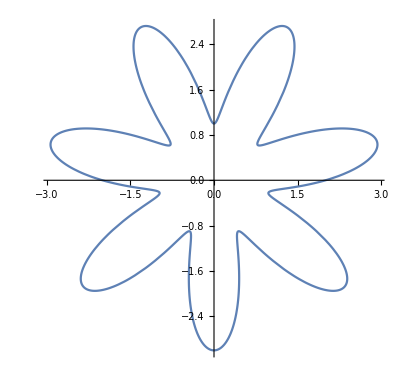

```mathematica
gamma = ParametricPlot[{(2+Sin[7t])Cos[t],(2+Sin[7t])Sin[t]},{t,0,2Pi}]
```

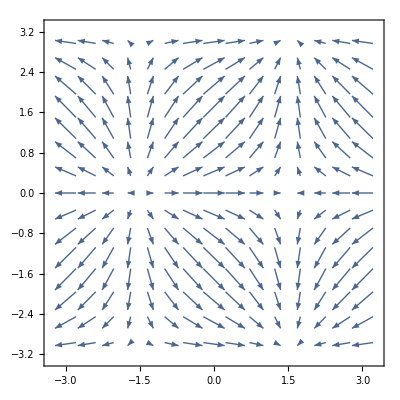

-Graphics-

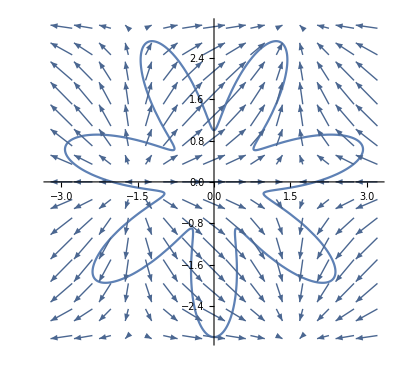

```mathematica
vtfield = VectorPlot[{Cos[x],Sin[y]},{x,-3,3},{y,-3,3}]
gamma = ParametricPlot[{(2+Sin[7t])Cos[t],(2+Sin[7t])Sin[t]},{t,0,2Pi}]
Show[gamma, vtfield, PlotRange -> All]
```

```mathematica
n =100
t[k_]:=2 *Pi* k/n
z[k_]:=(2+Sin[7t[k]])Cos[t[k]]+I (2+Sin[7t[k]])Sin[t[k]]
f[z_]:=Cos[Re[z]]- I Sin[Im[z]]
N[Sum[f[z[k]]*(z[k+1]-z[k]),{k,0,n-1}]]
```

100

0.0714602+5.91499 ⅈ